```mathematica
4!
```

24

```mathematica
Table[n!, {n,1,10}]
```

{1,2,6,24,120,720,5040,40320,362880,3628800}

```mathematica
Table[Prime[n], {n, 1, 100}]
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97,101,103,107,109,113,127,131,137,139,149,151,157,163,167,173,179,181,191,193,197,199,211,223,227,229,233,239,241,251,257,263,269,271,277,281,283,293,307,311,313,317,331,337,347,349,353,359,367,373,379,383,389,397,401,409,419,421,431,433,439,443,449,457,461,463,467,479,487,491,499,503,509,521,523,541}

Now find the number of primes between the factorials

```mathematica
primesBetween2Numbers = Select[Range[#1,#2], PrimeQ]&
```

Select[Range[#1,#2],PrimeQ]&

```mathematica
primesBetween2Numbers[2,6]
```

{2,3,5}

```mathematica
Partition[Table[n!, {n,1,10}],2,1]
```

{{1,2},{2,6},{6,24},{24,120},{120,720},{720,5040},{5040,40320},{40320,362880},{362880,3628800}}

```mathematica
primesBetweenFactorials = Apply[
primesBetween2Numbers, 
Partition[Table[n!, {n,1,#1}],2,1],
{1}
]&
```

Apply[primesBetween2Numbers,Partition[Table[n!,{n,1,#1}],2,1],{1}]&

```mathematica
Map[Length, {{1,2},{2}}]
```

{2,1}

```mathematica
Map[Length, primesBetweenFactorials[8]]
```

{1,3,6,21,98,547,3556}

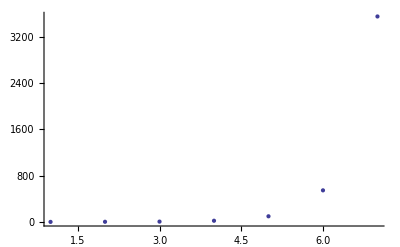

```mathematica
ListPlot[Map[Length, primesBetweenFactorials[8]]]
```

```mathematica
noOfPrimesBetweenFactorials = Map[Length, primesBetweenFactorials[8]]&
```

Length/@primesBetweenFactorials[8]&

```mathematica
noOfPrimesBetweenFactorials[5]
```

{1,3,6,21,98,547,3556}

```mathematica
FindFit[noOfPrimesBetweenFactorials[2], {a^x}, {a},x]
```

{a→3.1951}

```mathematica
Map[3.1951^#1&, {1,2,3}]
```

{3.1951,10.2087,32.6177}